#### Mass profiles:

Here  we  have  defined  the  mass  functions  for  a  uniform  sphere, minihalo, NFW  subhalo  and  boson  star . We provide the expressions normalised, so that M[R]=1, being R the radius of the EDO.

#### NFW sub - halo :

0.689814

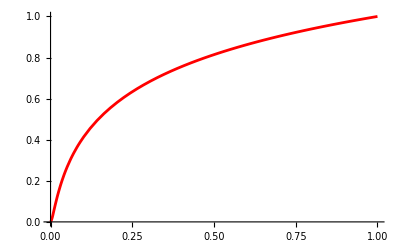

```mathematica
(* See Fig. 1 in https://arxiv.org/pdf/1805.00122.pdf *)
(*This result does not depend on the chosen RSbench; we define it to be 100 so that it can be solve numerically.*)
rSbench=100;ClearAll[mNFW];
rhoNFW[r_,rS_]=Piecewise[{{1/(r/rS(1+r/rS)^2),r≤100rS},{0,r>100 rS}}];
rhonfw[r_]=rhoNFW[r,rSbench];

mNFW[r_?NumberQ]:=NIntegrate[4 π rhonfw[rp] rp^2,{rp,0,r}]/NIntegrate[4 π rhonfw[rp] rp^2,{rp,0, 100 rSbench}];
r90NFW=r/.FindRoot[mNFW[r 100 rSbench]==0.9,{r,0.9}]
listNFW=Table[{rx,mNFW[rx]},{rx,0,100rSbench,50}];

NFWUnitary=Interpolation[listNFW];
Plot[NFWUnitary[x 100rSbench],{x,0,1},PlotStyle->Red]
0.6898142503158965
```

#### Boson star:

```mathematica
(* See Fig. 1 in https://arxiv.org/pdf/1805.00122.pdf *)
(*The value for rend does not affect the final result, we use 10 so that it can be solved numerically.*)
γ=-.69;
r0=10^-3.;
rend=10;
solBoson=NDSolve[{D[r χ[r],{r,2}]==2 r(Φ[r]-γ)χ[r],
D[r Φ[r],{r,2}]==r χ[r]^2,χ'[r0]==0,χ[r0]==1,χ[rend]==0,Φ'[r0]==0(*,WhenEvent[χ[r]<10^-1.,rMax=r;"StopIntegration"]*)},{χ,Φ},{r,r0,rend},Method->{"Shooting","StartingInitialConditions"->{Φ'[r0]==0,Φ[r0]==2 γ}}];
χ1[r_]=Evaluate[χ[r]/.solBoson[[1]]];
Mp=1.2209102930946626*^28 (*eV*);
MSun=1.1154947898498932*^66 (*eV*);
M1[m1_]= Mp^2/m1 NIntegrate[r^2 χ1[r]^2,{r,r0,rend}];

r90=rx/.FindRoot[NIntegrate[r^2 χ1[r]^2,{r,r0,rx}]/NIntegrate[r^2 χ1[r]^2,{r,r0,rend}]==.9,{rx,rend/10}][[1]]//Quiet;
r95=rx/.FindRoot[NIntegrate[r^2 χ1[r]^2,{r,r0,rx}]/NIntegrate[r^2 χ1[r]^2,{r,r0,rend}]==.95,{rx,rend/10}][[1]]//Quiet;

(* rescaling see https://arxiv.org/pdf/1805.00122.pdf *)
R95[λ_,m_]=λ^-1 r95/m;
Mλ[λ_,m_]:=λ M1[m];

r999=rx/.FindRoot[NIntegrate[r^2 χ1[r]^2,{r,r0,rx}]/NIntegrate[r^2 χ1[r]^2,{r,r0,rend}]==.999,{rx,rend/10}][[1]]//Quiet;

listbosm=Join[{{0,0}},Table[{rx,(Mp^2/1 NIntegrate[r^2 χ1[r]^2,{r,r0,rx }])/Mλ[1,1]},{rx,1/50,rend,1/50}]];
bosonUnitary=Interpolation[listbosm];
```

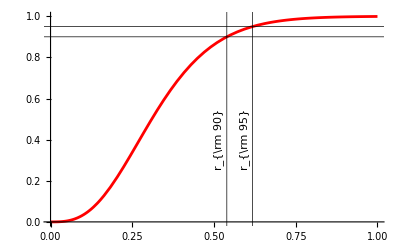

```mathematica
Plot[bosonUnitary[x r999],{x,0,1},PlotStyle->Red,FrameLabel->{"r","M(r)"},GridLines->{{r95/r999,r90/r999},{.9,.95}},GridLinesStyle->Black,Epilog->{Inset[Rotate["r_{\\rm 95}",90 Degree],{r95/r999-.025,0.4}],
Inset[Rotate["r_{\\rm 90}",90 Degree],{r90/r999-.025,0.4}]}]
```

```mathematica
r90/r999
```

0.539217

Uniform Sphere:

```mathematica
Mflat[r_]:=((r)^(3));
```

#### Ultracompact mini-halo:

```mathematica
Minihalo[r_]:=((r)^(3/4));
```

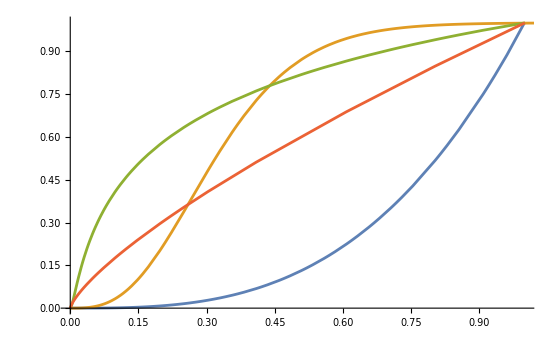

```mathematica
Plot[{Mflat[r ],bosmUnitary[r r999],NFWUnitary[r 100rSbench],Minihalo[r ],PlotRange->All},{r,0,10},PlotRange->{{0,1},{0,1}}]
```